```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{V[1]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "/home/riccardo/Programs/ABISS/models/SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{V[1]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts-3.11/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/ABISS/models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {/home/riccardo/Programs/ABISS/models/SMbgf_Anglerfish} initialized

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 48 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

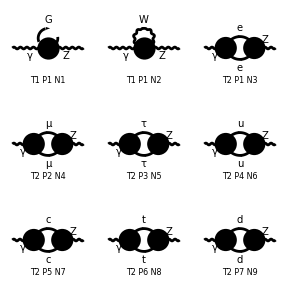

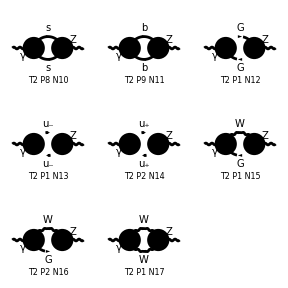

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/BGFSE/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
FullForm[myAmp1L[[1]]]
```

Times[Complex[0,Rational[1,16]],Power[EL,2],gFFAA,Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MW]],MetricTensor[Index[Lorentz,1],Index[Lorentz,2]],PolarizationVector[V[1],FourMomentum[Incoming,1],Index[Lorentz,1]],Conjugate[PolarizationVector][V[1],FourMomentum[Outgoing,1],Index[Lorentz,2]]]

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

-(SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]

```mathematica
t[Lor1_,Lor2_]=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

((SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]-SP[{Lor1},{Lor2}])/(-1+d)

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[1],p_,List[i_]]->1,Conjugate[PolarizationVector][V[1],p_,List[i_]]->1}
```

{ep[V[1],p_,{i_}]→1,ep^*[V[1],p_,{i_}]→1}

## Interference

```mathematica
myAmp1LABISS=Map[AmpSquare[#,1]&,myAmp1L];
```

```mathematica
myAmp1LnoEP=myAmp1LABISS/.removePolarizationVectors;
```

```mathematica
myAmp1LLongitudinal=Map[AmpSquare[#*l[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LTransverse=Map[AmpSquare[#*t[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
SquareSimplifyAndSave[myAmp1LnoEP*l[Lor1,Lor2],{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_8_1.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_9_1.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_10_1.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_11_1.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_12_1.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_13_1.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_14_1.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_15_1.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_16_1.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_17_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,17},{j,1}]
```

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_1_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_2_1.m.

Integral family {A0, {ME}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_3_1.m.

Integral family {A0, {MM}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_4_1.m.

Integral family {A0, {ML}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_5_1.m.

Integral family {A0, {MU}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_6_1.m.

Integral family {A0, {MC}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_7_1.m.

Integral family {A0, {MT}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_8_1.m.

Integral family {A0, {MD}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_9_1.m.

Integral family {A0, {MS}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_10_1.m.

Integral family {A0, {MB}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_11_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_12_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_13_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_14_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_15_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_16_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_17_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,17},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_17_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,-1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,-1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,-1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},1,-1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{m1},0,0]→0,userIntegral[A0,{m1},-1,1]→psq userIntegral[A0,{m1},1,0],userIntegral[A0,{m1},0,1]→userIntegral[A0,{m1},1,0],userIntegral[A0,{m1},1,-1]→psq userIntegral[A0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,-1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,-1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,-1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},1,-1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"RESULTS/Coefficients_"<>ToString[i]<>"_1.m")],{i,17}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gFFAA)/(16 π^4),0,0,0,0,0,0,0,0,0,0},{(ⅈ (-1+d) EL^2 gWWAA)/(8 π^4),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{(ⅈ EL^2 gFFA^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0},{-(ⅈ EL^2 ggmgmA^2)/(32 π^4),0,0,0,0,0,0,0,0,0,(ⅈ EL^2 ggmgmA^2 psq)/(64 π^4)},{-(ⅈ EL^2 ggpgpA^2)/(32 π^4),0,0,0,0,0,0,0,0,0,(ⅈ EL^2 ggpgpA^2 psq)/(64 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(16 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(16 π^4)},{(ⅈ EL^2 gWWA^2)/(8 π^4)+(ⅈ (-3+2 d) EL^2 gWWA^2)/(16 π^4),0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gWWA^2 (4 MW^2-psq))/(32 π^4)}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{(ⅈ EL^2 gFFA^2)/(8 π^4)-(ⅈ EL^2 gFFAA)/(16 π^4)-(ⅈ EL^2 ggmgmA^2)/(32 π^4)-(ⅈ EL^2 ggpgpA^2)/(32 π^4)+(ⅈ EL^2 gWWA^2)/(8 π^4)+(ⅈ (-3+2 d) EL^2 gWWA^2)/(16 π^4)+(ⅈ (-1+d) EL^2 gWWAA)/(8 π^4),0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(8 π^4)+(ⅈ EL^2 gWWA^2 (4 MW^2-psq))/(32 π^4)+(ⅈ EL^2 ggmgmA^2 psq)/(64 π^4)+(ⅈ EL^2 ggpgpA^2 psq)/(64 π^4)}

### Lagrangian parameter replace

```mathematica
parameterReplace={gFFA->1,gFFAA->2,ggmgmA->1,ggpgpA->1,gWWA->1,gWWAA->-1,gFAW->(-MW)}
```

{gFFA→1,gFFAA→2,ggmgmA→1,ggpgpA→1,gWWA→1,gWWAA→-1,gFAW→-MW}

```mathematica
coefficients/.parameterReplace//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0}